```mathematica
SetDirectory[NotebookDirectory[]]
```

/data2/users/sanderson/Research/KLStats/Isochrone/NoErrors/PermutationMethod

```mathematica
<<streams15x1000.mx
```

Conversion factor between km/s and kpc/Myr to a zillion (16) sigfigs

```mathematica
kmsTokpcMyr=0.001022729843472133;
```

Test with true potential parameters

```mathematica
radii=Sqrt[truePositions[[All,1]]^2+truePositions[[All,2]]^2+truePositions[[All,3]]^2];
```

```mathematica
nNN=10;
```

```mathematica
nf=Nearest[trueJrL[[All,{2,3}]]];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,trueJrL[[All,{2,3}]]];
trueSample= nNN/(π allNN^2)/Nstars;
```

```mathematica
ListPointPlot3D[Transpose[{trueJrL[[All,3]],trueJrL[[All,2]],trueSample}],PlotRange->All]
```

-Graphics3D-

```mathematica
Dimensions[shuffL=Transpose[{RandomSample[trueJrL[[All,2]]],trueJrL[[All,3]]}]]
```

{2000,2}

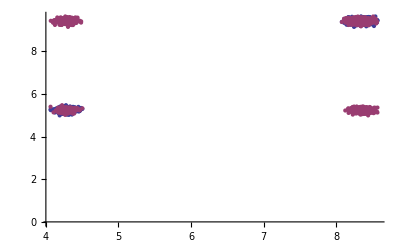

```mathematica
ListPlot[{Transpose[{trueJrL[[All,2]],trueJrL[[All,3]]}],shuffL}]
```

```mathematica
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/Nstars;
```

```mathematica
ListPointPlot3D[{Transpose[{trueJrL[[All,3]],trueJrL[[All,2]],trueSample}],Transpose[{trueJrL[[All,3]],trueJrL[[All,2]],smoothSample}]},PlotRange->All]
```

-Graphics3D-

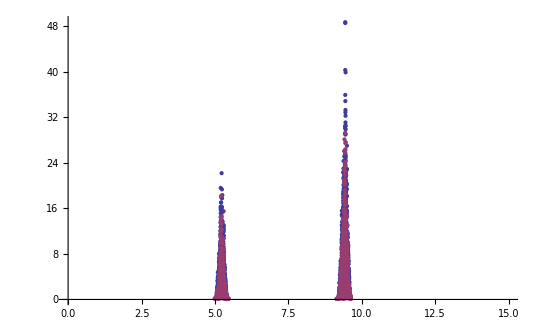

```mathematica
ListPlot[{Transpose[{trueJrL[[All,3]],trueSample}],Transpose[{trueJrL[[All,3]],smoothSample}]},PlotRange->{{0,15},All},PlotStyle->PointSize->Small]
```

```mathematica
Total[Log[trueSample/smoothSample]]/Nstars
```

0.633223

wrong actions -- trial

```mathematica
link=Install["/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math"]
```

LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math,14,10]

```mathematica
Mtrial=8.0;
btrial=8.0;
```

```mathematica
trialActions=MapThread[CartToAA[Mtrial, btrial,#1,#2]&,{ truePositions,trueVelocities}];
```

```mathematica
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions,goodSel];
nGood=Length[goodActions];
```

```mathematica
nf=Nearest[goodActions[[All,{2,3}]]];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions[[All,{2,3}]]];
trialSample= nNN/(π allNN^2)/nGood;
```

```mathematica
shuffL=Transpose[{RandomSample[goodActions[[All,2]]],goodActions[[All,3]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;
```

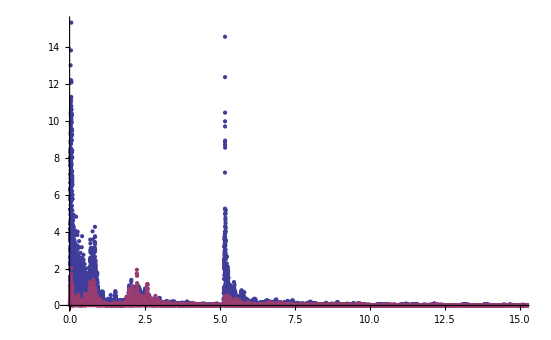

```mathematica
ListPlot[{Transpose[{goodActions[[All,3]],trialSample}],Transpose[{goodActions[[All,3]],smoothSample}]},PlotRange->{{0,15},All},PlotStyle->PointSize->Small]
```

```mathematica
Total[Log[trialSample/smoothSample]]/nGood
```

1.11831

exploring parameter space

```mathematica
Mt0=5.2;
bt0=0.0;
dM=1.0;
db=1.0;
MtMax=19.2;
btMax=16.0;
```

```mathematica
((MtMax-Mt0)/dM)((btMax-bt0)/db)
```

224.

```mathematica
KLStats={};
For[Mtrial=Mt0,Mtrial≤MtMax,Mtrial+=dM,For[btrial=bt0,btrial≤btMax,btrial+=db,
trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{truePositions,trueVelocities}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Nstars/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample= nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;
KLList=Log[trialSample/smoothSample];
AppendTo[KLStats,{Mtrial,btrial,Total[KLList]/nGood}],AppendTo[KLStats,{Mtrial,btrial,0}]];
]]
```

```mathematica
DumpSave["ShuffleTestCoarse10.mx",KLStats];
```

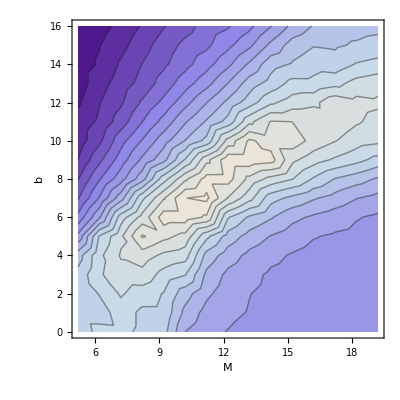

```mathematica
ListContourPlot[KLStats,Axes->True,AxesOrigin->{12.2,8.0},PlotRange->{0.1,All},Contours->Range[0.1,2,0.1],FrameLabel->{"M","b"}]
```

For loop in parallel

```mathematica
Mt0=5.2;
bt0=0.0;
dM=0.2;
db=0.2;
MtMax=19.2;
btMax=16.0;
```

```mathematica
((MtMax-Mt0)/dM)((btMax-bt0)/db)
```

5600.

```mathematica
ParallelEvaluate[$ProcessID]
```

{22474,22595,22713,22830}

```mathematica
ParallelEvaluate[$MachineName]
```

{galileo,galileo,galileo,galileo}

```mathematica
ParallelEvaluate[Install["/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math"]]
```

{LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math,10,2],LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math,10,2],LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math,10,2],LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/cartToAA/cartToAA_math,10,2]}

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{truePositions,trueVelocities}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Nstars/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample= nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,Mt0,MtMax,dM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{2624.81,{5751,3}}

```mathematica
DumpSave["ShuffleTestMed15.mx",KLStats];
```

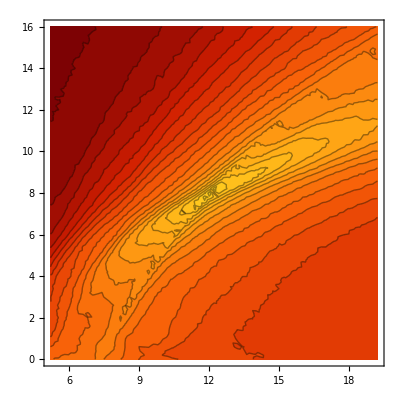

```mathematica
ListContourPlot[KLStats,Contours->Range[Round[Min[KLStats[[All,3]]],0.1],Round[Max[KLStats[[All,3]]],0.1],0.1],ContourLabels->None]
```

```mathematica
<<streams10x1000.mx
```

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{truePositions,trueVelocities}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Nstars/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample= nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,Mt0,MtMax,dM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{1539.55,{5751,3}}

```mathematica
DumpSave["ShuffleTestMed10.mx",KLStats];
```

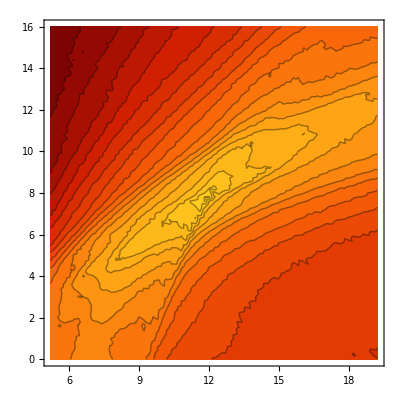

```mathematica
ListContourPlot[KLStats,Contours->Range[Round[Min[KLStats[[All,3]]],0.1],Round[Max[KLStats[[All,3]]],0.1],0.1],ContourLabels->None]
```

```mathematica
<<streams5x1000.mx
```

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{truePositions,trueVelocities}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Nstars/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample= nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,Mt0,MtMax,dM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{630.607,{5751,3}}

```mathematica
DumpSave["ShuffleTestMed5.mx",KLStats];
```

```mathematica
<<streams3x1000.mx
```

```mathematica
Timing[Dimensions[KLStats=Flatten[ParallelTable[{Mtrial,btrial,trialActions=MapThread[CartToAA[Mtrial, btrial, #1,#2]&,{truePositions,trueVelocities}];
goodSel=Thread[trialActions[[All,3]]>0];
goodActions=Pick[trialActions[[All,{2,3}]],goodSel];
nGood=Length[goodActions];
If[nGood>Nstars/2,
nf=Nearest[goodActions];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,goodActions];
trialSample= nNN/(π allNN^2)/nGood;
shuffL=Transpose[{RandomSample[goodActions[[All,1]]],goodActions[[All,2]]}];
nf=Nearest[shuffL];
allNN=Map[EuclideanDistance[Last[nf[#1,nNN+1]],#1]&,shuffL];
smoothSample=nNN/(π allNN^2)/nGood;Total[Log[trialSample/smoothSample]]/nGood,0]},{Mtrial,Mt0,MtMax,dM},{btrial,bt0,btMax,db},Method->"CoarsestGrained"],1]]]
```

{284.546,{5751,3}}

```mathematica
DumpSave["ShuffleTestMed3.mx",KLStats];
```

single-param scans

```mathematica
KLStatsbscanFine5=KLStats[[All,{2,3}]];
```

```mathematica
KLStatsMscanFine5=KLStats[[All,{1,3}]];
```

```mathematica
KLStatsMscan5=KLStats[[All,{1,3}]];
```

```mathematica
KLStatsbscan5=KLStats[[All,{2,3}]];
```

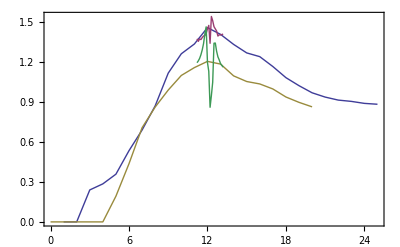

```mathematica
ListPlot[{KLStatsMscan5,KLStatsMscanFine5,KLStatsMscan,KLStatsMscanFine},AxesOrigin->{12.2,0},Frame->True,Joined->True]
```

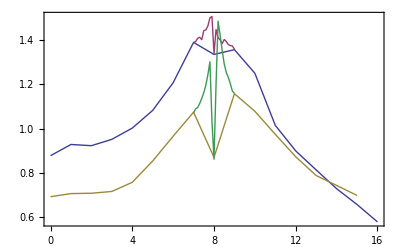

```mathematica
ListPlot[{KLStatsbscan5,KLStatsbscanFine5,KLStatsbscan,KLStatsbscanFine},AxesOrigin->{8.0,0},Frame->True,PlotRange->All,Joined->True]
```

```mathematica
DumpSave["shuffleTest.mx",{KLStatsMscan,KLStatsMscanFine,KLStatsbscan,KLStatsbscanFine}];
```

Plots with various numbers of streams

```mathematica
caption[ns_]:=Style[Text[Framed["N="<>ToString[ns]],Scaled[{0.9,0.12}],Background->White],FontSize->24,FontFamily->"Helvetica"]
```

```mathematica
SetOptions[ListContourPlot,Options[ListContourPlot]];
SetOptions[ListContourPlot,InterpolationOrder->1,ColorFunction->"SolarColors",ImageSize->400,PlotRange->{0,2.6},(*PlotRange->{1.2,2.5},ContourStyle->Thick,*)Contours->Range[0,2.6,0.1],FrameStyle->Directive[FontFamily->"Helvetica",FontSize->20],Axes->True,AxesOrigin->{12.2,8.0},AxesStyle->Thick,PlotRangePadding->None,ImagePadding->0,Frame->True,Ticks->None,ContourLabels->None(*(Style[Text[#3,{#1,#2}],Bold,White,FontFamily->"Helvetica",FontSize->16]&)*)];
```

```mathematica
KLMax={};
```

{0.315133}

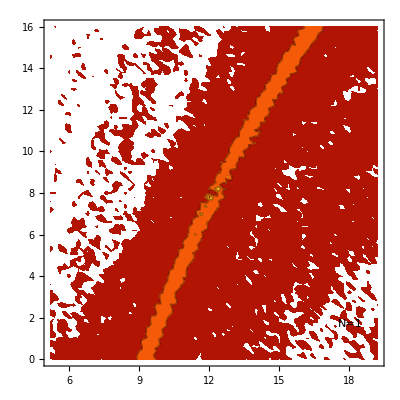

```mathematica
<<ShuffleTestMed1.mx
AppendTo[KLMax,Max[KLStats[[All,3]]]]
p1s=ListContourPlot[KLStats,Epilog->caption[1]]
```

{0.315133,0.949402}

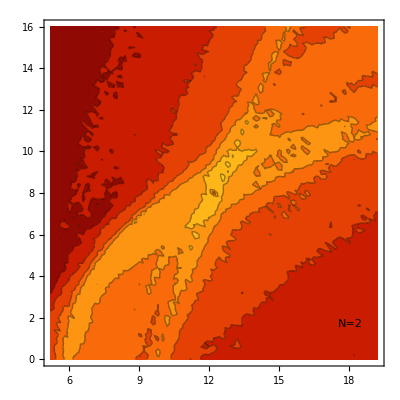

```mathematica
<<ShuffleTestMed2.mx
AppendTo[KLMax,Max[KLStats[[All,3]]]]
p2s=ListContourPlot[KLStats,Epilog->caption[2]]
```

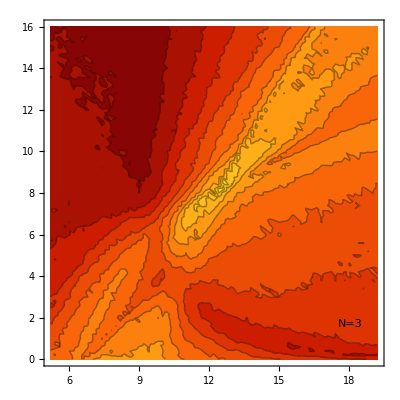

```mathematica
<<ShuffleTestMed3.mx
AppendTo[KLMax,Max[KLStats[[All,3]]]];
p3s=ListContourPlot[KLStats,Epilog->caption[3]]
```

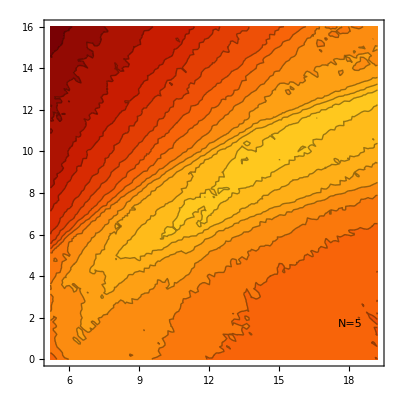

```mathematica
<<ShuffleTestMed5.mx
AppendTo[KLMax,Max[KLStats[[All,3]]]];
p5s=ListContourPlot[KLStats,Epilog->caption[5]]
```

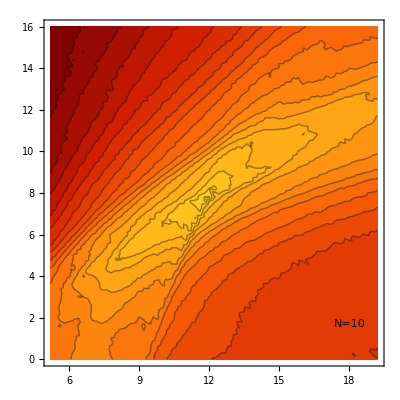

```mathematica
<<ShuffleTestMed10.mx
AppendTo[KLMax,Max[KLStats[[All,3]]]];
p10s=ListContourPlot[KLStats,Epilog->caption[10]]
```

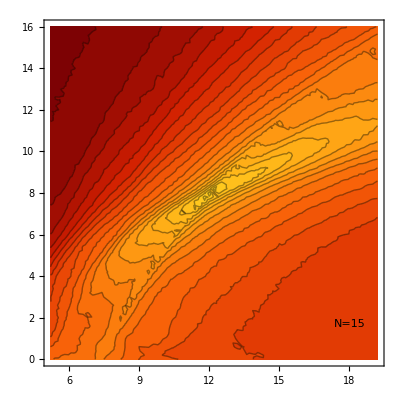

```mathematica
<<ShuffleTestMed15.mx
AppendTo[KLMax,Max[KLStats[[All,3]]]];
p15s=ListContourPlot[KLStats,Epilog->caption[15]]
```

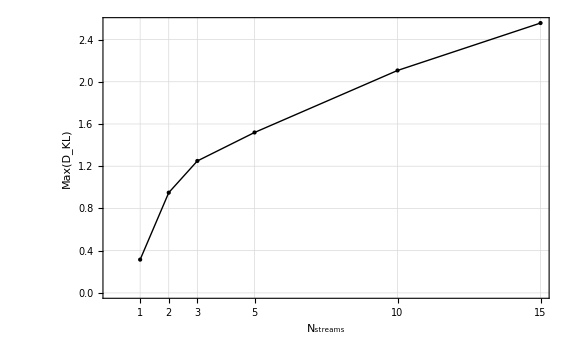

```mathematica
ListPlot[Transpose[{{1,2,3,5,10,15},KLMax}],Joined->True,PlotStyle->Directive[Thick,Black],Epilog->{PointSize[Large],Point[Transpose[{{1,2,3,5,10,15},KLMax}]]},Frame->True,FrameStyle->Directive[FontFamily->"Helvetica",FontSize->20],GridLines->Automatic,FrameLabel->{"N_streams","Max(D_KL)",None,None},FrameTicks->{{1,2,3,5,10,15},Automatic,Table[{n,""},{n,{1,2,3,5,10,15}}],Automatic}]
```

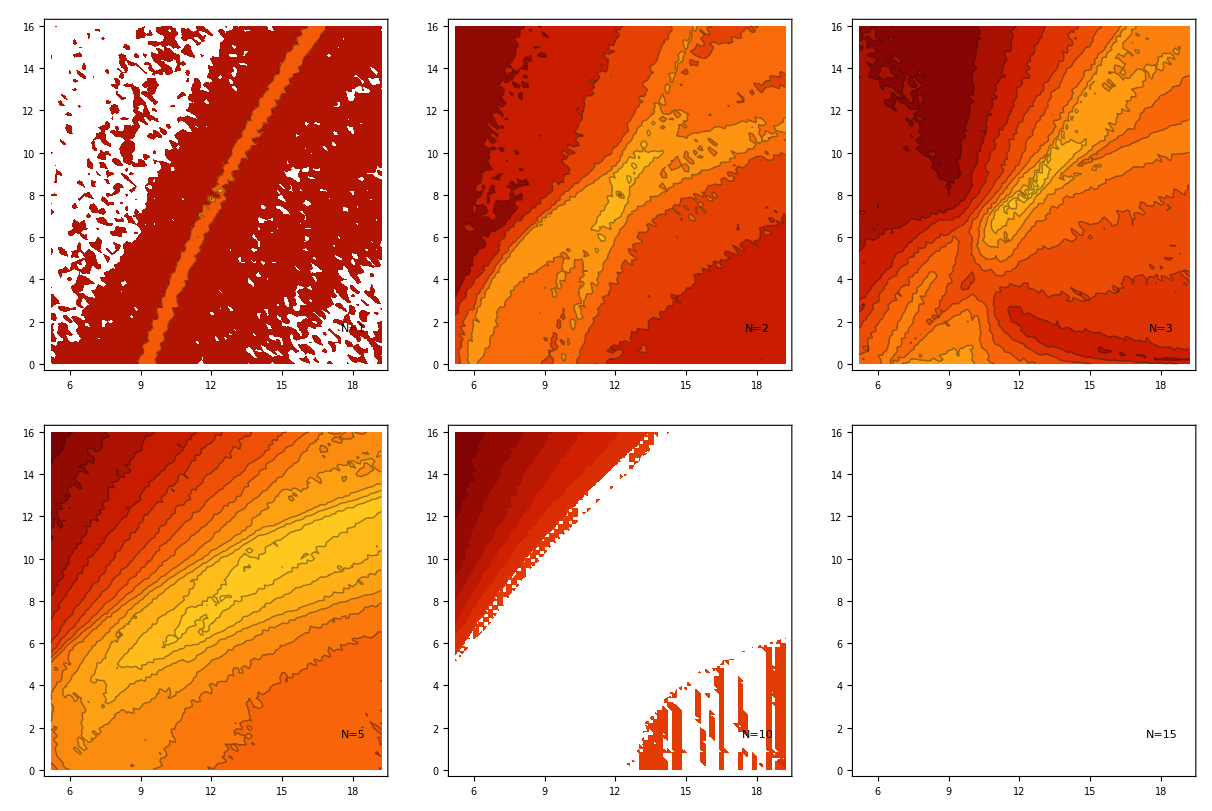

```mathematica
GraphicsGrid[{{p1s,p2s,p3s},{p5s,p10s,p15s}},Spacings->0]
```